```mathematica
(* shooting method applied to first order differential equation.  Give one boundary condition at endpoint of domain, find initial condition that produces this (if one exists) *)

deltax=.1;
alpha=2;
yvec={.1};
yvec1={.5};
xvec={};
For[i=1,i≤11,++i,
AppendTo[xvec,(i-1)*deltax]
];
For[i=1,i≤Length[xvec]-1,++i,
AppendTo[yvec,yvec[[i]]+alpha*(yvec[[i]]+alpha*yvec[[i]]*deltax/2)*deltax];
AppendTo[yvec1,yvec1[[i]]+alpha*(yvec1[[i]]+alpha*yvec1[[i]]*deltax/2)*deltax]
];
```

```mathematica
estint1=yvec[[1]]+(3-yvec[[11]])*(yvec1[[1]]-yvec[[1]])/(yvec1[[11]]-yvec[[11]]);
```

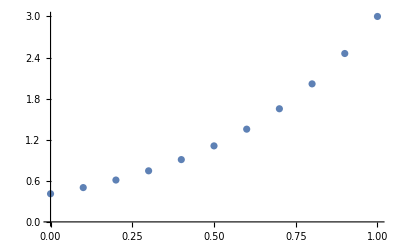

```mathematica
yvec2={estint1};
For[i=1,i≤Length[xvec]-1,++i,
AppendTo[yvec2,yvec2[[i]]+alpha*(yvec2[[i]]+alpha*yvec2[[i]]*deltax/2)*deltax]
];
list={};
For[i=1,i≤Length[xvec],++i,
AppendTo[list,{xvec[[i]],yvec2[[i]]}]
];
ListPlot[list]
```

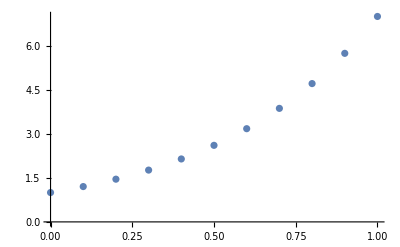

```mathematica
(**********************************************************************************)
(* shooting method applied to 2nd order ODE, y^(2)=4*y *)
(* We have y(0)=1, which is an initial condition for v(x)=dy/dx.  For dv/dx=d^2 y/dx^2=4*y, we do not have an initial condition, but know that we want y(1)=7.  So we guess initial conditions v(0) for the equation dv/dx=d^2 y/dx^2 and use the shooting method to try and "hit" y(1)=7.  We find two estimates that bracket the solution, and then use linear interpolation to find an estimate for v(0) that brings us as close as we need to go.  *) 

yvec={1};
yvec1={1};
vvec={1};
vvec1={3};
For[i=1,i≤10,++i,
AppendTo[yvec,yvec[[i]]+vvec[[i]]*deltax];
AppendTo[vvec,vvec[[i]]+4*(yvec[[i]]+4*yvec[[i]]*deltax/2)*deltax];
AppendTo[yvec1,yvec1[[i]]+vvec1[[i]]*deltax];
AppendTo[vvec1,vvec1[[i]]+4*(yvec1[[i]]+4*yvec1[[i]]*deltax/2)*deltax]
];
estint2= vvec[[1]]+(7-yvec[[11]])*(vvec1[[1]]-vvec[[1]])/(yvec1[[11]]-yvec[[11]]);
vvec2={estint2};
yvec2={1};
For[i=1,i≤10,++i,
AppendTo[yvec2,yvec2[[i]]+vvec2[[i]]*deltax];
AppendTo[vvec2,vvec2[[i]]+4*(yvec2[[i]]+4*yvec2[[i]]*deltax/2)*deltax]
];
list={};
For[i=1,i≤Length[xvec],++i,
AppendTo[list,{xvec[[i]],yvec2[[i]]}]
];
ListPlot[list]
```

```mathematica
(********************************************************************************)

xvec=Table[(i-1)*deltax,{i,11}];
uvec={0};
vvec={1};
uvec1={0};
vvec1={2};
For[i=1,i≤Length[xvec]-1,++i,
AppendTo[uvec,uvec[[i]]+vvec[[i]]*deltax];
AppendTo[vvec,vvec[[i]]+(-1)*(uvec[[i]]+(-1)*uvec[[i]]*deltax/2)*deltax];
AppendTo[uvec1,uvec1[[i]]+vvec1[[i]]*deltax];
AppendTo[vvec1,vvec1[[i]]+(-1)*(uvec1[[i]]+(-1)*uvec1[[i]]*deltax/2)*deltax];
];

estint3=vvec[[1]]+(Pi/2-uvec[[11]])*(vvec1[[1]]-vvec[[1]])/(uvec1[[11]]-uvec[[11]]);
vvec3={estint3};
uvec3={0};
For[i=1,i≤Length[xvec]-1,++i,
AppendTo[uvec3,uvec3[[i]]+vvec3[[i]]*deltax];
AppendTo[vvec3,vvec3[[i]]+(-1)*(uvec3[[i]]+(-1)*uvec3[[i]]*deltax/2)*deltax];
];

list={};
For[i=1,i≤Length[xvec],++i,
AppendTo[list,{xvec[[i]],uvec3[[i]]}]
];
```

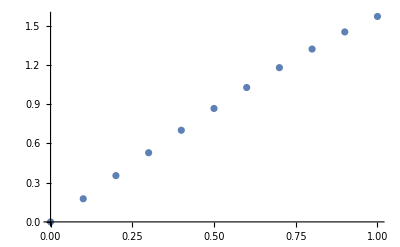

```mathematica
ListPlot[list]
```